```mathematica
Clear["Global`*"]
```

```mathematica
g[p_]=1-η*p;
g[p_]=1/(1+p*η);
u[i_,p_,q_] = -β*g[p]*i-c*p-θ*(p-q)^2;
BRD[i_,p_]=1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])])-p;
RD[i_,p_]=p*(1-p)*(u[i,1,p]-u[i,0,p]);
(* A couple different utility differences (between obeying or disobeying the norm. *)
SEIR={s'[t]==-β*g[p[t]]*s[t]*i[t],e'[t]==β*g[p[t]]*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*BRD[i[t],p[t]]};
ics={s[0]==0.99,e[0]==0,i[0]==0.01,p[0]==0.01};
SEIRS={s'[t]==-β*g[p[t]]*s[t]*i[t]+α*(1-s[t]-e[t]-i[t]),e'[t]==β*g[p[t]]*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*BRD[i[t],p[t]]};
ics={s[0]==0.99,e[0]==0,i[0]==0.01,p[0]==0.01};
```

```mathematica
eqs=FullSimplify[Solve[{-β*g[p]*s*i+α*(1-s-e-i)==0,β*g[p]*s*i-δ*e==0,δ*e-γ*i==0,ϵ*RD[i,p]==0},{s,e,i,p}]];
J=D[{-β*g[p]*s*i+α*(1-s-e-i),β*g[p]*s*i-δ*e,δ*e-γ*i,ϵ*RD[i,p]},{{s,e,i,p}}]/.eqs[[2;;7]];
eqs=eqs[[2;;7]];
```

```mathematica
(* For g(p) = 1/(1+ηx) *)
eqs=FullSimplify[Solve[{-β*g[p]*s*i+α*(1-s-e-i)==0,β*g[p]*s*i-δ*e==0,δ*e-γ*i==0,ϵ*RD[i,p]==0},{s,e,i,p}]];
J=D[{-β*g[p]*s*i+α*(1-s-e-i),β*g[p]*s*i-δ*e,δ*e-γ*i,ϵ*RD[i,p]},{{s,e,i,p}}]/.eqs;
```

```mathematica
Solve[u[i,1,p]-u[i,0,p]==0,i]
```

{{i→(c+θ-2 p θ)/(β (g[0]-g[1]))}}

```mathematica
(* Parameters *)
α=0.01;
β=0.41;
γ=0.1;
δ=0.2;
ϵ=4;
κ=100;
η=2;
```

```mathematica
M=Array[m,{10000,3}];
count=1;
Do[
M[[count]]={x/100,y/100,Dot[Boole[Map[AllTrue[#,#<0&,1]&,Map[Re[#]&,Map[Eigenvalues[#]&,J/.{θ->x/100,c->y/100}]]]]Boole[Map[AllTrue[#,And[0≤#≤ 1,MatchQ[#,_Real]]&,1]&,{s,e,i,p}/.eqs/.{θ->x/100,c->y/100}]],{32,16,8,4,2,1}]};
count=count+1;
,{x,1,100},{y,1,100}];
DeleteDuplicates[M[[All,3]]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0}.{32,16,8,4,2,1},{0,1,0,0,0,0,0,0,0,0,0,0,0}.{32,16,8,4,2,1},{0,1,0,1,0,0,0,0,0,0,0,0,0}.{32,16,8,4,2,1},{0,1,0,0,1,0,0,0,0,0,0,0,0}.{32,16,8,4,2,1}}

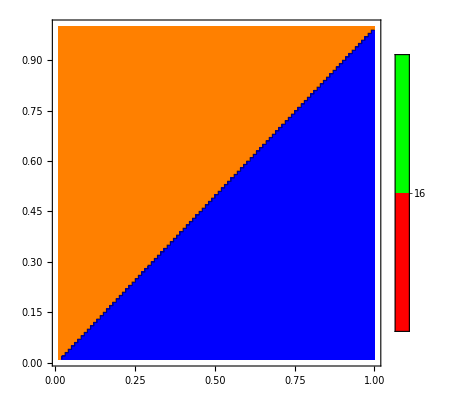

```mathematica
ListContourPlot[M,Contours->{0,4,12,20},ContourShading->{Blue,Red,Green,Orange},PlotLegends->Automatic]
```

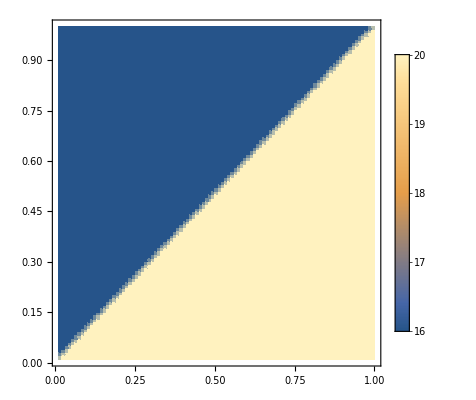

```mathematica
ListDensityPlot[M,PlotLegends->Automatic]
```

```mathematica
h1=Boole[Map[AllTrue[#,#<0&,1]&,Map[Re[#]&,Map[Eigenvalues[#]&,J/.{θ->80/100,c->20/100}]]]]
h2=Boole[Map[AllTrue[#,And[0≤#≤ 1,MatchQ[#,_Real]]&,1]&,{s,e,i,p}/.eqs/.{θ->80/100,c->20/100}]]
h1 h2
{s,e,i,p}/.eqs[[2;;7]]/.{θ->80/100,c->20/100}
Map[Eigenvalues[#]&,J/.{θ->80/100,c->20/100}]
```

{0,1,0,1,0,0}

{1,1,1,1,1,1}

{0,1,0,1,0,0}

{s,e,i,p}/.{{s→1.,e→0.,i→0.,p→0.},{s→0.243902,e→0.0328738,i→0.0657476,p→0.},{s→1.,e→0.,i→0.,p→1.},{s→0.439024,e→0.0243902,i→0.0487805,p→1.},{s→0.364626,e→0.027625,i→0.0552499,p→0.618708},{s→1.,e→0.,i→0.,p→0.625}}⟦2;;7⟧

{{-4.,-0.440689,0.140689,-0.01},{-3.95208+0. ⅈ,-0.306504+0. ⅈ,-0.0152261+0.0423199 ⅈ,-0.0152261-0.0423199 ⅈ},{-2.4,-0.369216,0.0692158,-0.01},{-2.43556+0. ⅈ,-0.302605+0. ⅈ,-0.00925285+0.0275482 ⅈ,-0.00925285-0.0275482 ⅈ},{1.50978+0. ⅈ,-0.303769+0. ⅈ,-0.0106736+0.0321118 ⅈ,-0.0106736-0.0321118 ⅈ},{1.5,-0.389096,0.0890955,-0.01}}

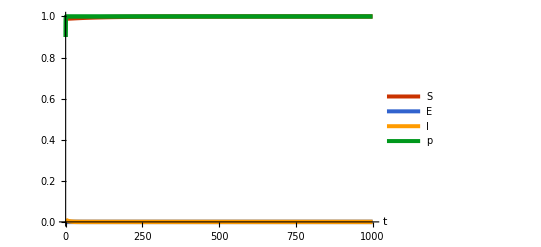

```mathematica
sol=NDSolve[Join[SEIRS/.{c->0.1,θ->0.8},{s[0]==0.99,e[0]==0,i[0]==0.01,p[0]==0.01}],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
```

```mathematica
sys={-β*ρ*s*i+α*(1-s-e-i),β*ρ*s*i-δ*e,δ*e-γ*i, ϵ*BRD[i,p]}
```

{(1-e-i-s) α-i s β ρ,-e δ+i s β ρ,-i γ+e δ,(1/(1+ⅇ^((c-i β+(i β)/(1+η)+(1-p)^2 θ-p^2 θ) κ))-p) ϵ}

```mathematica
J=D[sys,{{s,e,i,p}}]/.{s->1,e-> 0,i-> 0}
FullSimplify[Eigenvalues[J]]
CharacteristicPolynomial[J,λ]
FullSimplify[(γ+δ)^2+(γ-δ)^2+4 β δ ρ]
```

```mathematica
J=D[sys,{{s,e,i,p}}];
FullSimplify[Eigenvalues[J]]
CharacteristicPolynomial[J,λ]
```

{0,Root[α γ δ+i α β γ ρ+i α β δ ρ-s α β δ ρ+i β γ δ ρ+(α γ+α δ+γ δ+i α β ρ+i β γ ρ+i β δ ρ-s β δ ρ) #1+(α+γ+δ+i β ρ) #1^2+#1^3&,1],Root[α γ δ+i α β γ ρ+i α β δ ρ-s α β δ ρ+i β γ δ ρ+(α γ+α δ+γ δ+i α β ρ+i β γ ρ+i β δ ρ-s β δ ρ) #1+(α+γ+δ+i β ρ) #1^2+#1^3&,2],Root[α γ δ+i α β γ ρ+i α β δ ρ-s α β δ ρ+i β γ δ ρ+(α γ+α δ+γ δ+i α β ρ+i β γ ρ+i β δ ρ-s β δ ρ) #1+(α+γ+δ+i β ρ) #1^2+#1^3&,3]}

```mathematica
TeXForm[FullSimplify[-λ ((-γ-λ) (α δ+α λ+δ λ+λ^2+i α β ρ+i β δ ρ+i β λ ρ)-δ (i α β ρ-s α β ρ-s β λ ρ))]]
```

\lambda  (\gamma +\lambda ) ((\alpha +\lambda ) (\delta +\lambda )+\beta
    i \rho  (\alpha +\delta +\lambda ))-\beta  \delta  \lambda  \rho  (s
   (\alpha +\lambda )-\alpha  i)

```mathematica
FullSimplify[-λ ((-γ-λ) (α δ+α λ+δ λ+λ^2+i α β ρ+i β δ ρ+i β λ ρ)-δ (i α β ρ-s α β ρ-s β λ ρ))]
```

```mathematica
-β δ λ (-i α+s (α+λ)) ρ+λ (γ+λ) ((α+λ) (δ+λ)+i β (α+δ+λ) ρ)/.{s->1,i->0}
```

```mathematica
Solve[λ (α+λ) (γ+λ) (δ+λ)-β δ λ (α+λ) ρ==0,λ]
```

{{λ→0},{λ→-α},{λ→1/2 (-γ-δ-√(γ^2-2 γ δ+δ^2+4 β δ ρ))},{λ→1/2 (-γ-δ+√(γ^2-2 γ δ+δ^2+4 β δ ρ))}}

```mathematica
Solve[γ δ+γ λ+δ λ+λ^2-β δ ρ==0,λ]
```

{{λ→1/2 (-γ-δ-√(γ^2-2 γ δ+δ^2+4 β δ ρ))},{λ→1/2 (-γ-δ+√(γ^2-2 γ δ+δ^2+4 β δ ρ))}}

```mathematica
D[{-β*ρ[p]*s*i+α*(1-s-e-i),β*ρ[p]*s*i-δ*e,δ*e-γ*i, ϵ*F[i,p]},{{s,e,i,p}}]
```

```mathematica
TeXForm[MatrixForm[{{-α-i β ρ[p],-α,-α-s β ρ[p],-i s β ρ'[p]},{i β ρ[p],-δ,s β ρ[p],i s β ρ'[p]},{0,δ,-γ,0},{0,0,ϵ Derivative[1,0][F][i,p],ϵ Derivative[0,1][F][i,p]}}]]
```